# Quantile regression over weather time series

## Introduction

In this notebook we show two primary use cases of for Quantile Regression (QR):

Fitting regression quantiles over heteroscedastic data

Estimation of conditional density distributions

## Quantile regression over heteroscedastic data

Load the paclet

```mathematica
Needs["AntonAntonov`QuantileRegression`"]
```

Take temperature data

```mathematica
tsTemp=WeatherData[{"Atlanta","Georgia"},"Temperature",{{2018,1,1},{2023,1,1},"Day"}]
```

TimeSeries[…]

Plot time series points

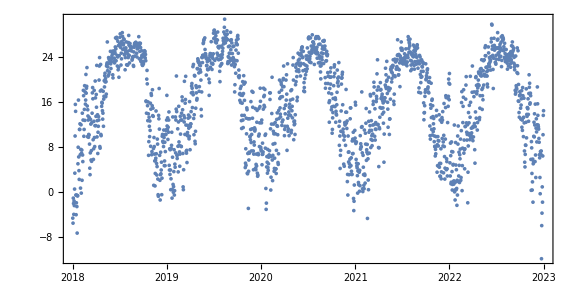

```mathematica
opts={ImageSize->Large,AspectRatio->1/2,PlotTheme->"Detailed",Joined->False};DateListPlot[tsTemp,opts]
```

Data summary

```mathematica
ResourceFunction["RecordsSummary"][tsTemp["Path"]]
```

{1 column 1
Min | 3.72375×10^9
1st Qu | 3.76317×10^9
Mean | 3.80264×10^9
Median | 3.80264×10^9
3rd Qu | 3.8421×10^9
Max | 3.88152×10^9,2 column 2
23.89 °C | 16
24.22 °C | 16
12.78 °C | 14
22.78 °C | 12
25 °C | 12
23.33 °C | 11
(Other) | 1746}

Find regression quantiles for 0.1, 0.5, 0.9

```mathematica
AbsoluteTiming[
probs={0.1,0.5,0.9};
qFuncs=QuantileRegression[QuantityMagnitude[tsTemp["Path"]],16,probs];
]
```

{1.0097,Null}

Plot time series points with fitted regression quantiles

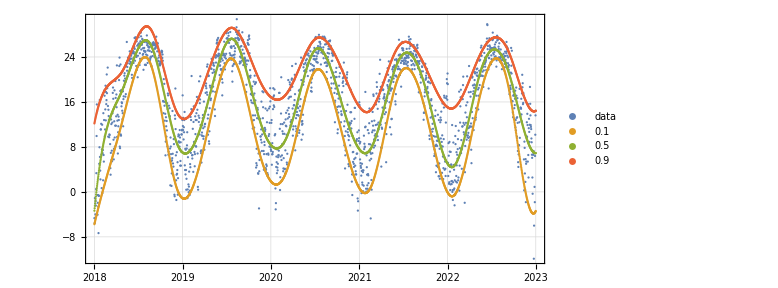

```mathematica
DateListPlot[{tsTemp["Path"],Map[Function[{f},{#,f[#]}&/@tsTemp["Times"]],qFuncs]},opts,Joined->{False,True,True,True},PlotLegends->{"data",Sequence@@probs}]
```

Remark: It should be obvious from the plot above that the time series data is heteroscedastic.

Count the number points under each surface

```mathematica
sepPoints=Association@MapThread[Function[{p,f},p->Length[Select[QuantityMagnitude[tsTemp["Path"]],#[[2]]<f[#[[1]]]&]]],{probs,qFuncs}]
```

<|0.1→182,0.5→915,0.9→1647|>

Show the corresponding fractions (should correspond to the probabilities)

```mathematica
sepFractions=N[sepPoints/Length[tsTemp["Path"]]]
```

<|0.1→0.0996169,0.5→0.500821,0.9→0.901478|>

## Estimation of conditional density distributions

Find regression quantiles for a "comprehensive" set of probabilities

```mathematica
AbsoluteTiming[
probs=Sort[Join[Range[0.1,0.9,0.1],{0.01,0.99}]];
qFuncs=QuantileRegression[QuantityMagnitude[tsTemp["Path"]],16,probs];
]
```

{2.31692,Null}

Plot time series points with fitted regression quantiles

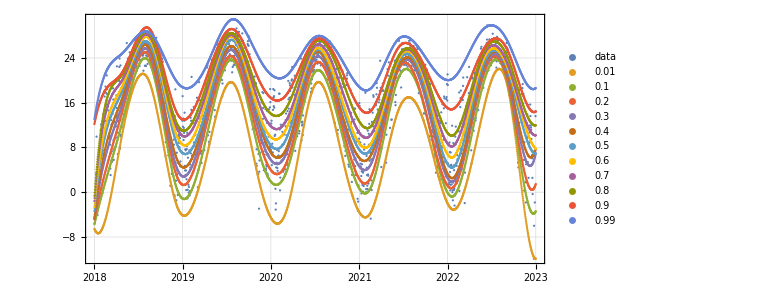

```mathematica
DateListPlot[{tsTemp["Path"],Map[Function[{f},{#,f[#]}&/@tsTemp["Times"]],qFuncs]},opts,Joined->{False,True,True,True},PlotLegends->{"data",Sequence@@probs}]
```

Reconstruct the CDF distribution at the focus point (January 1st, 2020)

```mathematica
focusPoint=AbsoluteTime[{2020,1,1}];
xs=Through[qFuncs[focusPoint]];
cdfPairs=Transpose[{xs,probs}];
```

Plot the empirical CDF

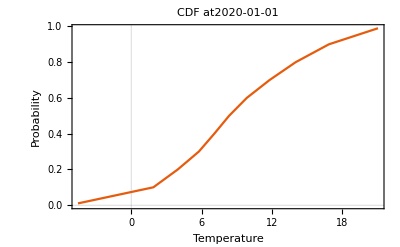

```mathematica
ListLinePlot[cdfPairs,]
```

In order to plot the corresponding PDF function define a CDF reconstruction function

```mathematica
CDFEstimate[t0_]:=CDFEstimate[probs,qFuncs,t0];
CDFEstimate[qs_,qFuncs_,t0_]:=Interpolation[Transpose[{Through[qFuncs[t0]],qs}],InterpolationOrder->1];
```

Plot empirical PDF

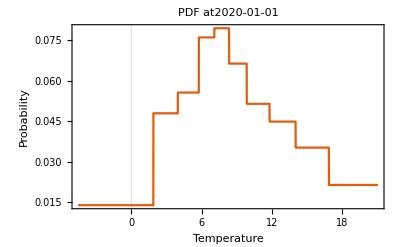

```mathematica
Plot[Evaluate@D[CDFEstimate[focusPoint][x],x],{x,Min[xs],Max[xs]},]
```

Related Guides

Quantile regression

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/QuantileRegression

AntonAntonov`QuantileRegression`

AntonAntonov/QuantileRegression/tutorial/Quantileregressionoverweathertimeseries

### Keywords

Quantile regression

Temperature data

Weather data

Heteroscedasticity

Heteroscedastic